```mathematica
a=-1/2;
b=1/2;
l1=1/4;
l2=1/4;
ld=1/2;
L=1;
ke=(G+Gf)/(1000);
kh=(G-Gf)/(1000);
ke1=(G+Gf+Vg)/(1000);
kh1=(G-Gf-Vg)/(1000);
eo1u=1;
ho1d=0;
ei2u=0;
hi2d=0;
γ1=γ2=γ;
ϵ=0.5;
Vg=0;
Z= (GM  - G - I*γ )*(GM+G + I*γ );
x = γ*(G + I*γ )/Z;
x1 = γ*(G + I *γ)/Z;
y = GM*γ/Z;
P=Solve[{eiLu==(1+I x)*eoLu-y*eiRu+I x*hoLd-y*hiRd,
eoRu==y*eoLu+(1+I x1)*eiRu+y*hoLd+I x1*hiRd,
hiLd==I x*eoLu-y*eiRu+(1+I x)*hoLd-y*hiRd,
hoRd==y*eoLu+I x1*eiRu+y*hoLd+(1+I x1)*hiRd,

ei1u==-(a+b)*eo1u+p*eo3u+p*ei5u,
hi1d==-(a+b)ho1d+p*ho3d+p*hi5d,
ei3u==p*eo1u+a*eo3u+b*ei5u,
hi3d==p*ho1d+a*ho3d+b*hi5d,
eo5u==p*eo1u+b*eo3u+a*ei5u,
ho5d==p*ho1d+b*ho3d+a*hi5d,

eo2u==-(a+b)ei2u+p*ei4u+p*eo6u,
ho2d==-(a+b)hi2d+p*hi4d+p*ho6d,
eo4u==p*ei2u+a*ei4u+b*eo6u,
ho4d==p*hi2d+a*hi4d+b*ho6d,
ei6u==p*ei2u+b*ei4u+a*eo6u,
hi6d==p*hi2d+b*hi4d+a*ho6d,

ei5u==Exp[I*ke*l1]*Exp[-I*ϕ*l1]eiLu,
eoLu==Exp[I*ke*l1]*Exp[I*ϕ*l1]eo5u,
hi5d==Exp[I*kh*l1]*Exp[I*ϕ*l1]hiLd,
hoLd==Exp[I*kh*l1]*Exp[-I*ϕ*l1]ho5d,
eo6u==Exp[I*ke*l2]*Exp[I*ϕ*l2]eoRu,
eiRu==Exp[I*ke*l2]*Exp[-I*ϕ*l2]ei6u,
ho6d==Exp[I*kh*l2]*Exp[-I*ϕ*l2]hoRd,
hiRd==Exp[I*kh*l2]*Exp[I*ϕ*l2]hi6d,
eo3u==Exp[I*ke1*ld]*Exp[I*ϕ*ld]eo4u,
ei4u==Exp[I*ke1*ld]*Exp[-I*ϕ*ld]ei3u,
ho3d==Exp[I*kh1*ld]*Exp[-I*ϕ*ld]ho4d,
hi4d==Exp[I*kh1*ld]*Exp[I*ϕ*ld]hi3d}

,{eiLu,eoLu,eiRu,hoLd,hiRd,eoRu,hiLd,hoRd,ei1u,eo3u,ei5u,hi1d,ho3d,hi5d,ei3u,hi3d,eo5u,ho5d,eo2u,ei4u,eo6u,ho2d,hi4d,ho6d,eo4u,ho4d,ei6u,hi6d}];
ei1u=ei1u/.P[[1]];
hi1d=hi1d/.P[[1]];
eo2u=eo2u/.P[[1]]
ho2d=ho2d/.P[[1]]
```

(4 ⅇ^((ⅈ ϕ)/2) (4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G^2 p^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G^2 p^2+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) G^2 p^2-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM^2 p^2-8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) GM^2 p^2-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+ⅈ ϕ) GM^2 p^2-2 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+4 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ-2 ⅈ ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2 γ+8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ-4 ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+ⅈ ϕ) G p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000) GM p^2 γ+2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) GM p^2 γ+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000) GM p^2 γ-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2 γ-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((ⅈ G)/500+(ⅈ Gf)/500+2 ⅈ ϕ) GM p^2 γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/400+2 ⅈ ϕ) GM p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-4 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ^2-ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2+ⅇ^((ⅈ G)/400+(3 ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ^2))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2)

-((4 ⅇ^((ⅈ G)/2000) γ (-ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) G p^2+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) G p^2+2 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) G p^2+ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) G p^2+ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+3 ⅈ ϕ) G p^2-ⅈ ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+3 ⅈ ϕ) G p^2-ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) G p^2-2 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2+4 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM p^2+2 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM p^2-2 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) GM p^2+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) p^2 γ-2 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) p^2 γ-2 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ+ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) p^2 γ))/(16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) G^2+16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G^2-16 ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) GM^2-16 ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) GM^2-8 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+2 ⅈ ϕ) G γ+32 ⅈ ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) G γ+16 ⅈ ⅇ^((ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+2 ⅈ ϕ) G γ-8 ⅈ ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ-4 ⅇ^((3 ⅈ G)/2000+(ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ G)/2000+(3 ⅈ Gf)/2000+3 ⅈ ϕ) GM γ+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+3 ⅈ ϕ) GM γ+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ^2-16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+8 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2-2 ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+2 ⅈ ϕ) γ^2+4 ⅇ^((ⅈ G)/1000+(ⅈ Gf)/500+2 ⅈ ϕ) γ^2+ⅇ^((ⅈ G)/500+(ⅈ Gf)/1000+4 ⅈ ϕ) γ^2))

```mathematica
Te=Refine[eo2u]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ (G+Gf+1000 ϕ))/2000) (4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 ⅈ ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) G γ+ⅇ^((ⅈ G)/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) GM γ+2 ⅇ^((ⅈ (3 G+Gf))/2000) GM γ-ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) GM γ-4 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) GM γ-ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) GM γ-2 ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) GM γ+ⅇ^((ⅈ (2 G+Gf+1000 ϕ))/1000) (-2 ⅈ G-γ) γ-ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) γ^2+ⅇ^((ⅈ (2 G+Gf+3000 ϕ))/1000) γ^2+ⅇ^((ⅈ G)/1000+ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-ⅈ G γ)+4 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+8 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+4 ⅇ^((ⅈ (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
Th=Refine[ho2d]/.{p->Sqrt[1/2]}//Simplify
```

(2 ⅇ^((ⅈ G)/2000+ⅈ ϕ) γ (-ⅈ ⅇ^((ⅈ (G+Gf))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf))/1000) G-2 ⅈ ⅇ^((ⅈ (G+2 Gf))/1000) G-2 ⅈ ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) G-ⅈ ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) G+ⅈ ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) G+2 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM-4 ⅇ^((ⅈ Gf)/1000+ⅈ ϕ) GM-2 ⅇ^((ⅈ (G+Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM-2 ⅇ^((ⅈ (G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM+2 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM+ⅇ^((3 ⅈ (G+Gf))/2000) (-ⅈ G-γ)+ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) (-ⅈ G-γ)+ⅈ ⅇ^((ⅈ (3 G+Gf))/2000) (G+ⅈ γ)+ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) (G+ⅈ γ)+2 ⅇ^((ⅈ (G+3 Gf))/2000) (-ⅈ G+γ)+2 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (-ⅈ G+γ)))/(-8 ⅈ ⅇ^((ⅈ (3 G+Gf+4000 ϕ))/2000) G γ-8 ⅈ ⅇ^((ⅈ (3 G+3 Gf+4000 ϕ))/2000) G γ+4 ⅇ^((ⅈ G)/1000+ⅈ ϕ) GM γ-4 ⅇ^((ⅈ G)/1000+3 ⅈ ϕ) GM γ+4 ⅇ^((3 ⅈ (G+Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (3 G+Gf+2000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 ⅇ^((ⅈ (G+2 Gf+3000 ϕ))/1000) GM γ-4 ⅇ^((ⅈ (3 G+Gf+6000 ϕ))/2000) GM γ-4 ⅇ^((ⅈ (G+2 (Gf+500 ϕ)))/1000) GM γ+ⅇ^((ⅈ (2 G+Gf))/1000) γ^2-2 ⅇ^((ⅈ (2 G+Gf+2000 ϕ))/1000) γ^2+ⅇ^((ⅈ (2 G+Gf+4000 ϕ))/1000) γ^2+4 ⅇ^((ⅈ G)/1000+2 ⅈ ϕ) γ (-2 ⅈ G+γ)+4 ⅇ^((ⅈ (G+2 Gf+2000 ϕ))/1000) γ (-2 ⅈ G+γ)+16 ⅇ^((ⅈ (G+Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+ⅈ G γ)+16 ⅇ^((ⅈ Gf)/1000+2 ⅈ ϕ) (G^2-GM^2+2 ⅈ G γ-γ^2)+8 ⅇ^((ⅈ (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
ϕ=1.57;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[γ=-9.99,γ<=50.01,γ=γ+1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,γ,P,z0,Nmax,k,Pmaxr}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check221.dat",list]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.999952+0. ⅈ and 6.7663×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.00010304+0. ⅈ and 0.0000479005 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in G near {G} = {3.97126}. NIntegrate obtained 0.00010304+0. ⅈ and 0.0000479005 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

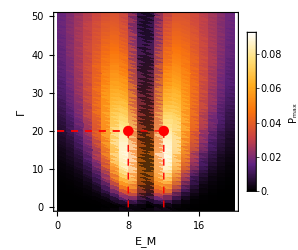
-Graphics-(a)

```mathematica
data1=Import["check221.dat"][[All,{1,2,3}]];
data2=Import["check221.dat"][[All,{1,2,4}]];
data3=Import["check221.dat"][[All,{1,2,5}]];
data4=Import["check221.dat"][[All,{1,2,6}]];
data5=Import["check221.dat"][[All,{1,2,7}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

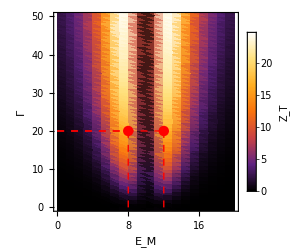
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["Z_T",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

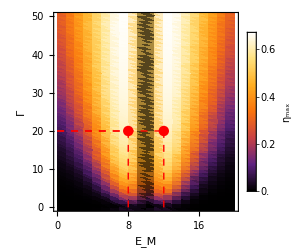
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

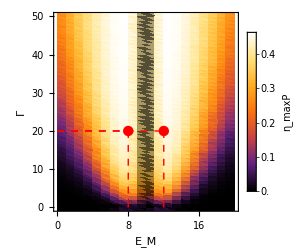
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data4,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_maxP",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,20},{8,20}},{{0,20},{12,20}},{{8,20},{8,0}},{{12,20},{12,0}}}],PointSize[0.03],Point[{{8,20},{12,20}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig.2.pdf",A5,ImageResolution->300]
```

fig.2.pdf

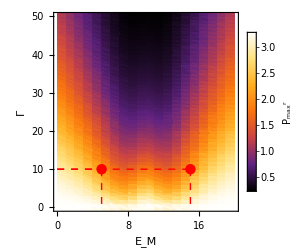
-Graphics-(a)

```mathematica
A1=Labeled[ListDensityPlot[data5,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

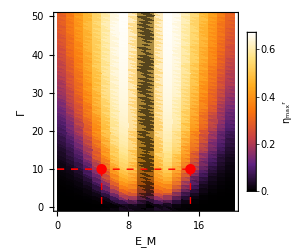
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["Γ",24,Black,FontFamily->"Chilanka"]},PlotRange->{{0,20},{0,50},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,10},{5,10}},{{0,10},{15,10}},{{5,10},{5,0}},{{15,10},{15,0}}}],PointSize[0.03],Point[{{5,10},{15,10}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1},{A2}},Frame->All]
```

-Graphics-(a)
-Graphics-(b)

```mathematica
Export["fig.4.pdf",A5,ImageResolution->300]
```

fig.4.pdf

```mathematica
T1=Abs[(2 E^((I (G+Gf+1000 ϕ))/2000) (4 E^((I (G+2 (Gf+500 ϕ)))/1000) (G^2-GM^2)-4 I E^((I (3 G+Gf+2000 ϕ))/2000) G γ+E^((I G)/1000) GM γ+E^((I (2 G+Gf))/1000) GM γ+2 E^((I (3 G+Gf))/2000) GM γ-E^((I G)/1000+2 I ϕ) GM γ-4 E^((I Gf)/1000+2 I ϕ) GM γ-E^((I (2 G+Gf+2000 ϕ))/1000) GM γ+4 E^((I (G+2 Gf+2000 ϕ))/1000) GM γ-4 E^((I (G+Gf+4000 ϕ))/2000) GM γ-2 E^((I (3 G+Gf+4000 ϕ))/2000) GM γ+4 E^((I (3 G+3 Gf+4000 ϕ))/2000) GM γ+E^((I (2 G+Gf+1000 ϕ))/1000) (-2 I G-γ) γ-E^((I G)/1000+3 I ϕ) γ^2+E^((I (2 G+Gf+3000 ϕ))/1000) γ^2+E^((I G)/1000+I ϕ) γ (-2 I G+γ)+4 E^((I (3 G+3 Gf+2000 ϕ))/2000) (G^2-GM^2-I G γ)+4 E^((I (G+Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+8 E^((I (G+3 Gf+2000 ϕ))/2000) (G^2-GM^2+I G γ)+4 E^((I Gf)/1000+I ϕ) (G^2-GM^2+2 I G γ-γ^2)+4 E^((I (G+Gf+1000 ϕ))/1000) (2 G^2-2 GM^2+γ^2)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2+Abs[(2 E^((I G)/2000+I ϕ) γ (-I E^((I (G+Gf))/1000) G+I E^((I (2 G+Gf))/1000) G-2 I E^((I (G+2 Gf))/1000) G-2 I E^((I G)/1000+2 I ϕ) G-I E^((I (G+Gf+2000 ϕ))/1000) G+I E^((I (2 G+Gf+2000 ϕ))/1000) G+2 E^((I G)/1000+I ϕ) GM-4 E^((I Gf)/1000+I ϕ) GM-2 E^((I (G+Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+Gf+2000 ϕ))/2000) GM-2 E^((I (G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM+2 E^((I (G+2 (Gf+500 ϕ)))/1000) GM+E^((3 I (G+Gf))/2000) (-I G-γ)+E^((I (3 G+Gf+4000 ϕ))/2000) (-I G-γ)+I E^((I (3 G+Gf))/2000) (G+I γ)+I E^((I (3 G+3 Gf+4000 ϕ))/2000) (G+I γ)+2 E^((I (G+3 Gf))/2000) (-I G+γ)+2 E^((I (G+Gf+4000 ϕ))/2000) (-I G+γ)))/(-8 I E^((I (3 G+Gf+4000 ϕ))/2000) G γ-8 I E^((I (3 G+3 Gf+4000 ϕ))/2000) G γ+4 E^((I G)/1000+I ϕ) GM γ-4 E^((I G)/1000+3 I ϕ) GM γ+4 E^((3 I (G+Gf+2000 ϕ))/2000) GM γ+4 E^((I (3 G+Gf+2000 ϕ))/2000) GM γ-4 E^((I (3 G+3 Gf+2000 ϕ))/2000) GM γ+4 E^((I (G+2 Gf+3000 ϕ))/1000) GM γ-4 E^((I (3 G+Gf+6000 ϕ))/2000) GM γ-4 E^((I (G+2 (Gf+500 ϕ)))/1000) GM γ+E^((I (2 G+Gf))/1000) γ^2-2 E^((I (2 G+Gf+2000 ϕ))/1000) γ^2+E^((I (2 G+Gf+4000 ϕ))/1000) γ^2+4 E^((I G)/1000+2 I ϕ) γ (-2 I G+γ)+4 E^((I (G+2 Gf+2000 ϕ))/1000) γ (-2 I G+γ)+16 E^((I (G+Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I (G+3 Gf+4000 ϕ))/2000) (G^2-GM^2+I G γ)+16 E^((I Gf)/1000+2 I ϕ) (G^2-GM^2+2 I G γ-γ^2)+8 E^((I (G+Gf+2000 ϕ))/1000) (2 G^2-2 GM^2+γ^2))]^2;
Gf=10;
γ=20;
kbT=1;
SetSharedVariable[list1]
list1={};
ParallelDo[{
For[ϕ=-6.38,ϕ<=6.28,ϕ=ϕ+0.1;
{df=(ⅇ^((G-10)/kbT)/((1+ⅇ^((G-10)/kbT))^2 kbT));
LeTt=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LeVv=( ((G- (Gf))/kbT)^(0)) (T1)(df);
LhVv=( ((G - (Gf))/kbT)^(1)) (T1)(df);
LhTt=( ((G - (Gf))/kbT)^(2)) (T1)(df);

LeV= NIntegrate[ LeVv, {G, -Infinity, Infinity}];

LeT= NIntegrate[LeTt , {G, -Infinity, Infinity}];

LhV= NIntegrate[LhVv        , {G, -Infinity, Infinity}];

LhT= NIntegrate[LhTt , {G, -Infinity, Infinity}];
P=Re[ (1/(4*1)) * ((LeT)^2)/LeV];
kappa= ((LeV*LhT - LhV*LeT)/ (LeV))/3.285;
S = -LeT/LeV;
z0=11.5Re[ (LeV(S)^2/(kappa))/(1)];
Nmax=Re[(Sqrt[z0  + 1] - 1)/(Sqrt[z0 + 1] + 1)];
k=Re[0.5*z0/(z0+2)];
Pmaxr= Re[Sqrt[(LhT)(LeV*LhT - LhV*LeT)/(LeV)]];
list=AppendTo[list1,{GM,ϕ,P,z0,Nmax,k,Pmaxr}];
}];
},{GM,0.,20,1}];//AbsoluteTiming
list=Sort[list1];
Export["check220.dat",list]
```

{1045.32,Null}

check220.dat

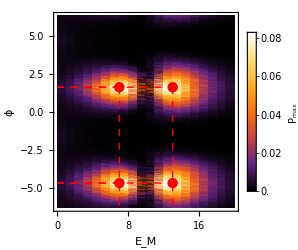
-Graphics-(a)

```mathematica
data1=Import["check220.dat"][[All,{1,2,3}]];
data2=Import["check220.dat"][[All,{1,2,4}]];
data3=Import["check220.dat"][[All,{1,2,5}]];
data4=Import["check220.dat"][[All,{1,2,6}]];
data5=Import["check220.dat"][[All,{1,2,7}]];
Needs["PlotLegends`"]
A1=Labeled[ListDensityPlot[data1,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

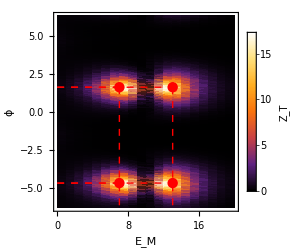
-Graphics-(c)

```mathematica
A3=Labeled[ListDensityPlot[data2,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["Z_T",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(c)",Bottom,LabelStyle->Directive[Black,25]]
```

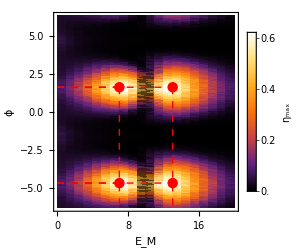
-Graphics-(d)

```mathematica
A4=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(d)",Bottom,LabelStyle->Directive[Black,25]]
```

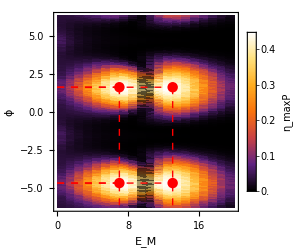
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data4,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_maxP",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1.62},{7,1.62}},{{0,1.62},{13,1.62}},{{0,-4.68},{7,-4.68}},{{0,-4.68},{13,-4.68}},{{7,1.62},{7,-6.28}},{{13,1.62},{13,-6.28}}}],PointSize[0.03],Point[{{7,1.62},{13,1.62},{7,-4.68},{13,-4.68}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1,A2},{A3,A4}},Frame->All]
```

-Graphics-(a) | -Graphics-(b)
-Graphics-(c) | -Graphics-(d)

```mathematica
Export["fig.3.pdf",A5,ImageResolution->300]
```

fig.3.pdf

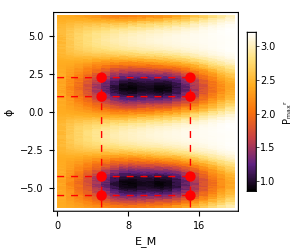
-Graphics-(a)

```mathematica
A1=Labeled[ListDensityPlot[data5,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["P_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1},{15,1}},{{0,2.25},{15,2.25}},{{0,-4.25},{15,-4.25}},{{0,-5.50},{15,-5.50}},{{5,-6.28},{5,2.25}},{{15,-6.28},{15,2.25}}}],PointSize[0.03],Point[{{5,1},{15,1},{5,-4.25},{15,-4.25},{5,2.25},{15,2.25},{5,-5.5},{15,-5.5}}]}],"(a)",Bottom,LabelStyle->Directive[Black,25]]
```

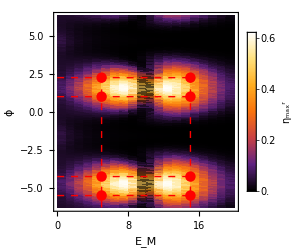
-Graphics-(b)

```mathematica
A2=Labeled[ListDensityPlot[data3,ImageSize->250,ColorFunction->ColorData["SunsetColors"],PlotLegends->Placed[BarLegend[ Automatic,LegendLabel->Style["η_max^r",24,Black]],Right],FrameLabel->{Style["E_M",24,Black],Style["ϕ",24,Black]},PlotRange->{{0,20},{-6.28,6.28},All},ClippingStyle->Automatic,RotateLabel->False,Epilog->{Red,Dashed,Line[{{{0,1},{15,1}},{{0,2.25},{15,2.25}},{{0,-4.25},{15,-4.25}},{{0,-5.50},{15,-5.50}},{{5,-6.28},{5,2.25}},{{15,-6.28},{15,2.25}}}],PointSize[0.03],Point[{{5,1},{15,1},{5,-4.25},{15,-4.25},{5,2.25},{15,2.25},{5,-5.5},{15,-5.5}}]}],"(b)",Bottom,LabelStyle->Directive[Black,25]]
```

```mathematica
A5=Grid[{{A1},{A2}},Frame->All]
```

-Graphics-(a)
-Graphics-(b)

```mathematica
Export["fig.5.pdf",A5,ImageResolution->300]
```

fig.5.pdf